# 28 Feb and 1 Mar 2017 NW GaAs mesa 1200/100 and 1200/65

```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
ClearAll[feb28]
feb28=Table[Import[path<>"\\Data\\2017\\feb\\28\\28feb_acuun_"<>ToString[i]<>".dat"],{i,1,16}];
ClearAll[mar1]
mar1=Table[Import[path<>"\\Data\\2017\\mar\\1\\1mar_accun_"<>ToString[i]<>".dat"],{i,1,12}];
```

```mathematica
ClearAll[allDat,short1200100,long1200100,short120065, long120065,marLong1200100,febLong1200100]
short1200100 = {"short1200100",feb28[[{1,4,5,8,9,12}]]};
long1200100 = {"long1200100",feb28[[{3,6,7,10,11}]]};
short120065 = {"short120065",mar1[[{1,4,5,8,9}]]};
long120065 = {"long120065",mar1[[{2,3,6,7}]]};
marLong1200100 = {"marLong1200100",mar1[[{11,12}]]};
febLong1200100 = {"febLong1200100",feb6[[{14,17,18}]]};
allDat={short1200100,long1200100,short120065, long120065,marLong1200100,febLong1200100};
feb6=Table[Import[path<>"\\Data\\2017\\feb\\6\\6feb_acuun_"<>ToString[i]<>".dat"],{i,1,20}];
```

```mathematica
ClearAll[powerDatDict]
powerDatDict = 
<|
"short1200100"->{1,0.5,2,4,.63,.19},
"long1200100"->{0.5,2,4,.63,.19},
"short120065"->{1,2,4,6,1.5},
"long120065"->{1,2,4,6},
"febLong1200100"->{0.5,1,2},
"marLong1200100"->{1,2}
|>;
```

```mathematica
TableForm[Table[Table[allDat[[j]][[2,i]][[1,1]],{i,Length[allDat[[j,2]]]}],{j,Length[allDat]}]]
```

-101.5 | -101.5 | -101.5 | -101.5 | -101.5 | -101.5
-101. | -101. | -101. | -101. | -101. | 
-101.5 | -101.5 | -101.5 | -101.5 | -101.5 | 
-101. | -101. | -101. | -101. |  | 
-101. | -101. |  |  |  | 
-101.5 | -101.5 | -101.5 |  |  |

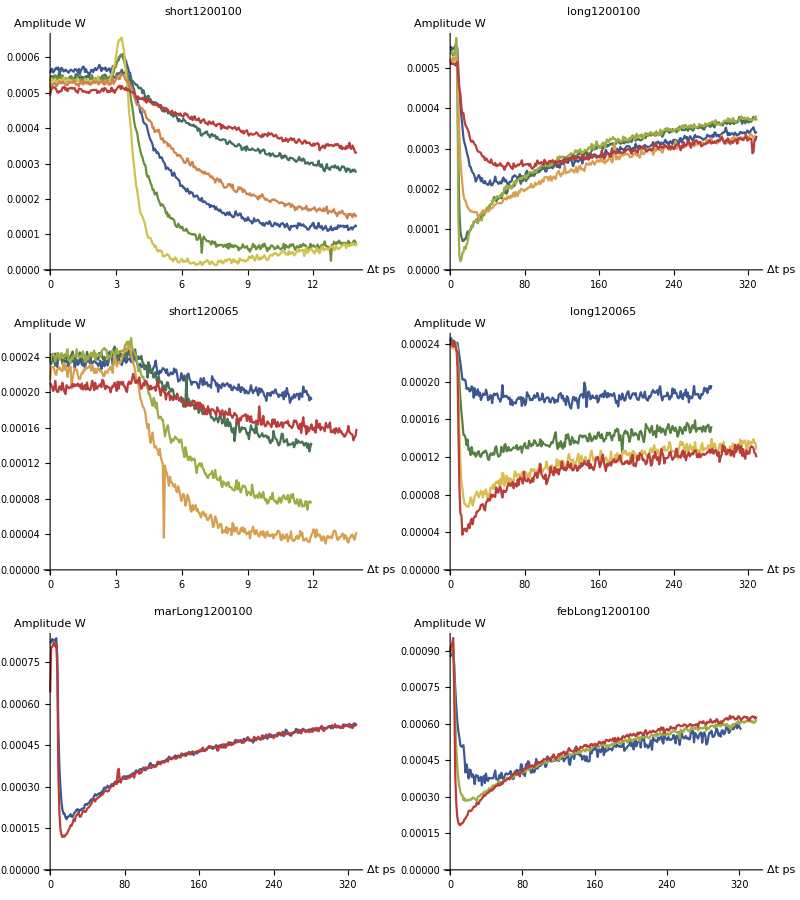

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
Table[dat[[2,i]][[All,{3,2}]],{i,1,Length[dat[[2]]]}],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->dat[[1]],
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All],
{dat,allDat}],
2]
]
```

```mathematica
amplitudes=
Table[
{
dat[[1]],
Table[
MeanFilter[
(dat[[2]][[i,All,2]]+(Max[Mean/@dat[[2]][[All,2;;4,2]]]-Mean[dat[[2]][[i,2;;4,2]]]))/Mean/@Max[dat[[2]][[All,2;;4,2]]],
1],
{i,1,Length[dat[[2]]]}]
},
{dat,allDat}];
```

```mathematica
normDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],amplitudes[[i,2]][[j]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

```mathematica
Keys[powerDatDict]
```

{short1200100,long1200100,short120065,long120065,febLong1200100,marLong1200100}

```mathematica
TableForm[
Table[
Rasterize[
ListLinePlot[
normDatDic[name],
ImageSize->600,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"Δt пс","ΔE_(:0422:0413:0446)/E"},
FrameStyle->Directive[Black, Thick,18],
PlotStyle-> Table[Directive[ColorData["DarkRainbow"][i],AbsoluteThickness[3]],{i,0,1,1/(Length[normDatDic[name]]-1)}],
PlotRange->All,
PlotLegends->(Style["C_(:043f) = "<>ToString[#]<>"×10^15 (:0441:043c)^-3",16]& )/@powerDatDict[name]]
],
{name,Keys[powerDatDict]}]
]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Keys[powerDatDict]
```

{short1200100,long1200100,short120065,long120065,febLong1200100,marLong1200100}

```mathematica
normLogDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],Log[amplitudes[[i,2]][[j]]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

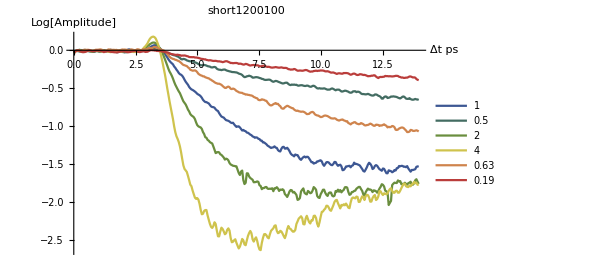
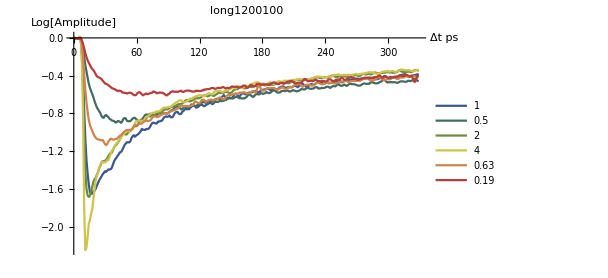
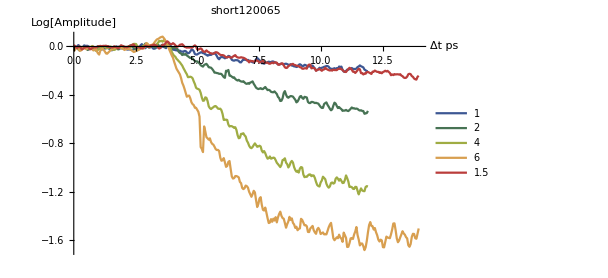
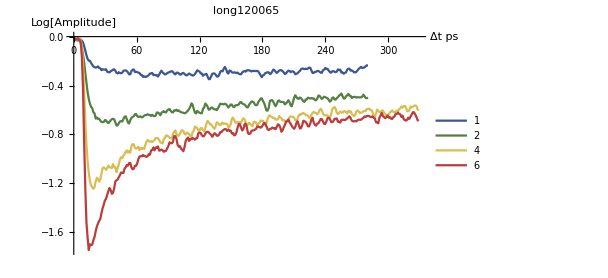
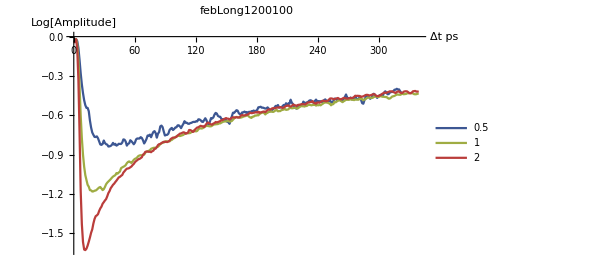
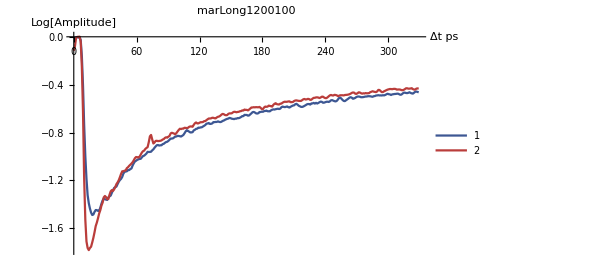
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
normLogDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Log[Amplitude]"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict[name]],
{name,Keys[powerDatDict]}],
2]
]
```

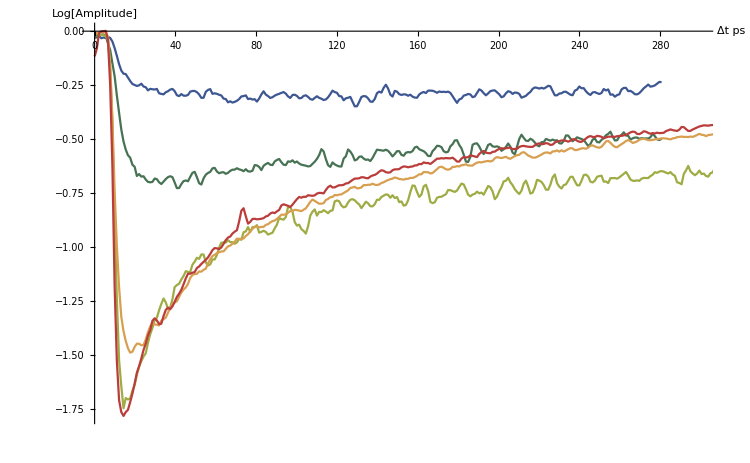

```mathematica
ListLinePlot[
Join[normLogDatDic["long120065"][[{1,2,4}]],normLogDatDic["marLong1200100"][[{1,2}]]],
ImageSize->750,
AxesLabel->{"Δt ps","Log[Amplitude]"},
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->{{0,300},All}
]
```

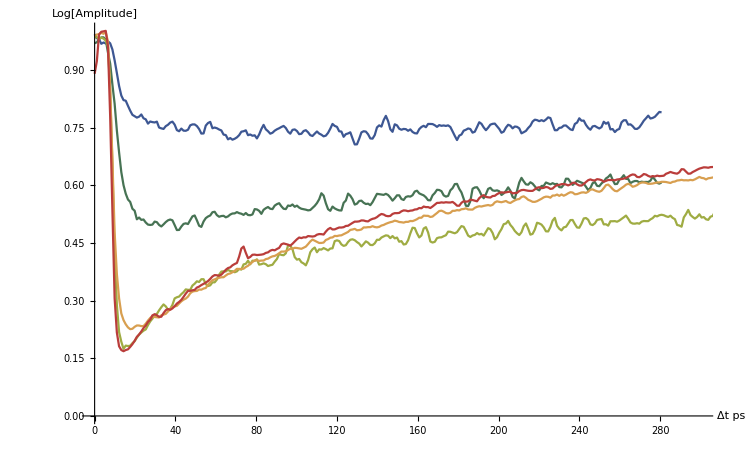

```mathematica
ListLinePlot[
Join[normDatDic["long120065"][[{1,2,4}]],normDatDic["marLong1200100"][[{1,2}]]],
ImageSize->750,
AxesLabel->{"Δt ps","Log[Amplitude]"},
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->{{0,300},All}
]
```

#### Feb 8

```mathematica
Min[normLogDatDic["febLong1200100"][[2]][[All,2]]]/Min[normLogDatDic["febLong1200100"][[3]][[All,2]]]
```

0.72559

#### Feb 28

```mathematica
Min[normLogDatDic["long1200100"][[1]][[All,2]]]/Min[normLogDatDic["long1200100"][[3]][[All,2]]]
```

0.980602

#### Mar 1

```mathematica
Min[normLogDatDic["marLong1200100"][[1]][[All,2]]]/Min[normLogDatDic["marLong1200100"][[2]][[All,2]]]
```

0.835506